```mathematica
Clear[Veff]
```

```mathematica
Veff[L_,r_,M_,g_,l_]:=L^2/r^2(1-2M g^2/(r^2+g^2)^(3/2)+r^2/l^2);
```

```mathematica
Solve[(1+rh^2/l^2)(rh^2+g^2)^(3/2)/2/rh^2==M,rh]
```

{{rh→-√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,1]},{rh→√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,1]},{rh→-√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,2]},{rh→√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,2]},{rh→-√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,3]},{rh→√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,3]},{rh→-√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,4]},{rh→√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,4]},{rh→-√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,5]},{rh→√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,5]}}

```mathematica
{
√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,1],
√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,2],
√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,3],
√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,4],
√Root[g^6 l^4+(2 g^6 l^2+3 g^4 l^4) #1+(g^6+6 g^4 l^2+3 g^2 l^4-4 l^4 M^2) #1^2+(3 g^4+6 g^2 l^2+l^4) #1^3+(3 g^2+2 l^2) #1^4+#1^5&,5]
}/.{M->2,g->3,l->6}//N
```

{0.+1.78618 ⅈ,1.70856-6.96643 ⅈ,1.70856+6.96643 ⅈ,2.03518-2.53669 ⅈ,2.03518+2.53669 ⅈ}

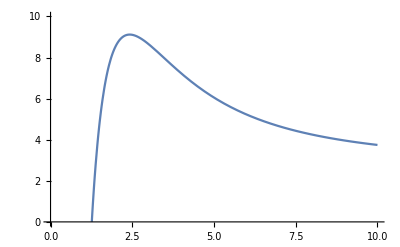

```mathematica
Plot[Veff[10,r,2,3,6],{r,0.01,10},AxesOrigin->{0,0},PlotRange->{{0,10},{0,10}}]
```